# Fox Model Reproduction

```mathematica
(* Notebook parameters: *)
DoExports={False,False,False, False}; (* Export the results from the notebook onto disk. 1: S and S_int, 2: Metabolite conservations, 3: Reactions Rates, 4: Net Reactions *)
ModelYear="2022" (* Which model to run: choose 2020 or 2022 *)
DoZeroConcentrationTest=False; (* Checks whether the concentrations of all metabolies is zero given that the initial conditions are zero *)
On[Assert]; (* Turn on assertions *)
```

2022

## Set Up the Fox Model Equations, Parameters and Initial Conditions

Step 1: Import ODEs (parsed using script and saved in Mathematica form).

```mathematica
(* Import the .xls and run the parsing function *)
importedODEs=Import[FileNameJoin[{NotebookDirectory[], "data/FAS/YEAR_fox_ODEs.csv"}]//StringReplace["YEAR"->ModelYear], "csv"];
ODEs = Flatten[ToExpression/@importedODEs];
ODEs[[1;;2]](* Check if the import worked *)
```

{y1'[t]==-k11f e1[t] y1[t]+k11r y83[t],y2'[t]==-k12f y2[t] y83[t]+k12r y84[t]}

Step 2: Get the variables in the model.

```mathematica
(* This is another 'pure function' that works over a list. It converts the left had side of the equation ('#[[1]]') to a string, and drops the last four characters. Then it joins the remaining string (just the variable) with '[t]' and converts the total into an expression. Essentially: y'[t] -> y[t] *)
vars=ToExpression[StringJoin[StringDrop[ToString[#[[1]]],-4],"[t]"]]&/@ODEs;
```

Step 3: Get the enzyme total equations for the model and define the total number of each enzyme.

```mathematica
importedEnzymeEqs=Flatten[Import[FileNameJoin[{NotebookDirectory[], "data/FAS/YEAR_fox_enzyme_totals.csv"}]//StringReplace["YEAR"->ModelYear], "csv"]];
enzymeEqs=ToExpression[importedEnzymeEqs];
enzymeTotalVals ={
e1tot->0, (* acc*)
e2tot->1, (* fabd *)
e3tot->1, (* fabh *)
e4tot->1, (* fabg *)
e5tot->1, (* fabz *)
e6tot->1, (* fabi *)
e7tot->10, (* tesa *)
e8tot->1, (* fabf *)
e9tot->1, (* faba *)
e10tot->1  (* fabb *)
};
enzymeEqs[[3]]
```

e3[t]→e3tot-y110[t]-y111[t]-y125[t]-y126[t]-y140[t]-y141[t]-y155[t]-y156[t]-y170[t]-y171[t]-y185[t]-y186[t]-y200[t]-y201[t]-y215[t]-y216[t]-y224[t]-y225[t]-y239[t]-y240[t]-y254[t]-y255[t]-y269[t]-y270[t]-y284[t]-y285[t]-y293[t]-y90[t]-y91[t]-y92[t]-y95[t]-y96[t]

Step 4: Make the ODEs independent of the time dependent enzyme concentration.

```mathematica
ODEsNoEnz=ODEs/.enzymeEqs;
ODEsNoEnz[[1]]
```

y1'[t]==k11r y83[t]-k11f y1[t] (e1tot-y83[t]-y84[t]-y85[t]-y86[t])

Step 5: Import the kinetic parameters from the Excel sheet. Note that k11f is k1_1f, etc. The inhibitory kinetic parameters and the unsaturated FA parameters are separate.

```mathematica
importedKinParams=Import[FileNameJoin[{NotebookDirectory[], "data/FAS/YEAR_fox_kinetic_params.csv"}]//StringReplace["YEAR"->ModelYear],"csv"];
(* From the import create rule 'k1_1f, x' to 'k11f -> x' for each element along the rows *)
kinParams = ToExpression[StringReplace[ToString[#[[1]]], "_"->""]]->#[[2]]&/@importedKinParams;
(* Check the ODEs filled in with the kinetic parameters *)
ODEs[[1;;5]]//TableForm
ODEs[[1;;5]]/.kinParams // TableForm
ODEsNoEnz[[1;;5]]/.kinParams/.enzymeTotalVals//TableForm
```

y1'[t]==-k11f e1[t] y1[t]+k11r y83[t]
y2'[t]==-k12f y2[t] y83[t]+k12r y84[t]
y3'[t]==-k104f e10[t] y3[t]-k31f e3[t] y3[t]-k84f e8[t] y3[t]+k104r y305[t]+k84r y308[t]-k13f y3[t] y85[t]+k13r y86[t]+k31r y90[t]
y4'[t]==kcat71 y101[t]+k82f1 y102[t]+k102f1 y107[t]+kcat72 y116[t]+k82f2 y117[t]+k102f2 y122[t]+kcat73 y131[t]+k82f3 y132[t]+k102f3 y137[t]+kcat74 y146[t]+k82f4 y147[t]+k102f4 y152[t]+kcat75 y161[t]+k82f5 y162[t]+k102f5 y167[t]+kcat76 y176[t]+k82f6 y177[t]+k102f6 y182[t]+kcat77 y191[t]+k82f7 y192[t]+k102f7 y197[t]+kcat78 y206[t]+k82f8 y207[t]+k102f8 y212[t]+kcat79 y221[t]+kcat75 y230[t]+k82f5 y231[t]+k102f5 y236[t]+kcat76 y245[t]+k82f6 y246[t]+k102f6 y251[t]+kcat77 y260[t]+k82f7 y261[t]+k102f7 y266[t]+kcat78 y275[t]+k82f8 y276[t]+k102f8 y281[t]+kcat79 y290[t]+k3inhr y293[t]+k4inhr y294[t]+k5inhr y295[t]+k6inhr y296[t]+k7inhr y297[t]+k8inhr y298[t]+k9inhr y299[t]+k10inhr y300[t]+k102f4 y302[t]+k109f y313[t]+k89f y315[t]-k10inhf e10[t] y4[t]-k3inhf e3[t] y4[t]-k4inhf e4[t] y4[t]-k5inhf e5[t] y4[t]-k6inhf e6[t] y4[t]-k7inhf e7[t] y4[t]-k8inhf e8[t] y4[t]-k9inhf e9[t] y4[t]-k82r1 y103[t] y4[t]-k102r1 y108[t] y4[t]-k82r2 y118[t] y4[t]-k102r2 y123[t] y4[t]-k82r3 y133[t] y4[t]-k102r3 y138[t] y4[t]-k82r4 y148[t] y4[t]-k102r4 y153[t] y4[t]-k82r5 y163[t] y4[t]-k102r5 y168[t] y4[t]-k82r6 y178[t] y4[t]-k102r6 y183[t] y4[t]-k82r7 y193[t] y4[t]-k102r7 y198[t] y4[t]-k82r8 y208[t] y4[t]-k102r8 y213[t] y4[t]-k82r5 y232[t] y4[t]-k102r5 y237[t] y4[t]-k82r6 y247[t] y4[t]-k102r6 y252[t] y4[t]-k82r7 y262[t] y4[t]-k102r7 y267[t] y4[t]-k82r8 y277[t] y4[t]-k102r8 y282[t] y4[t]-k102r4 y303[t] y4[t]-k109r y306[t] y4[t]-k89r y309[t] y4[t]-k23f y4[t] y88[t]+k23r y89[t]
y5'[t]==-k41f1 e4[t] y5[t]+k41r1 y93[t]

y1'[t]==-5.06765 e1[t] y1[t]+75.9768 y83[t]
y2'[t]==-0.0303907 y2[t] y83[t]+75.9768 y84[t]
y3'[t]==0.-284.947 e10[t] y3[t]-284.947 e3[t] y3[t]+11397.9 y305[t]-3.03907 y3[t] y85[t]+75.9768 y86[t]+11397.9 y90[t]
y4'[t]==0.0330538 y101[t]+1411.1 y102[t]+1411.1 y107[t]+0.0296204 y116[t]+1411.1 y117[t]+1411.1 y122[t]+0.0602301 y131[t]+1411.1 y132[t]+1411.1 y137[t]+0.00919455 y146[t]+1411.1 y147[t]+1411.1 y152[t]+0.146973 y161[t]+1411.1 y162[t]+1411.1 y167[t]+0.266636 y176[t]+1411.1 y177[t]+1411.1 y182[t]+0.581934 y191[t]+1411.1 y192[t]+1411.1 y197[t]+0.710541 y206[t]+1411.1 y207[t]+1411.1 y212[t]+0.894316 y221[t]+0.146973 y230[t]+1411.1 y231[t]+1411.1 y236[t]+0.266636 y245[t]+1411.1 y246[t]+1411.1 y251[t]+0.581934 y260[t]+1411.1 y261[t]+1411.1 y266[t]+0.710541 y275[t]+1411.1 y276[t]+1411.1 y281[t]+0.894316 y290[t]+0.09157 y293[t]+0.09157 y294[t]+0.09157 y295[t]+0.09157 y296[t]+0.09157 y297[t]+0.09157 y298[t]+0.09157 y299[t]+0.09157 y300[t]+1411.1 y302[t]+1411.1 y313[t]+1411.1 y315[t]-0.00241 e10[t] y4[t]-0.0007 e3[t] y4[t]-0.00241 e4[t] y4[t]-0.00241 e5[t] y4[t]-0.00241 e6[t] y4[t]-0.00241 e7[t] y4[t]-0.0007 e8[t] y4[t]-0.00241 e9[t] y4[t]-402.139 y103[t] y4[t]-402.139 y108[t] y4[t]-402.139 y118[t] y4[t]-402.139 y123[t] y4[t]-402.139 y133[t] y4[t]-402.139 y138[t] y4[t]-402.139 y148[t] y4[t]-402.139 y153[t] y4[t]-402.139 y163[t] y4[t]-402.139 y168[t] y4[t]-402.139 y178[t] y4[t]-402.139 y183[t] y4[t]-402.139 y193[t] y4[t]-402.139 y198[t] y4[t]-402.139 y208[t] y4[t]-402.139 y213[t] y4[t]-402.139 y232[t] y4[t]-402.139 y237[t] y4[t]-402.139 y247[t] y4[t]-402.139 y252[t] y4[t]-402.139 y262[t] y4[t]-402.139 y267[t] y4[t]-402.139 y277[t] y4[t]-402.139 y282[t] y4[t]-402.139 y303[t] y4[t]-402.139 y306[t] y4[t]-402.139 y309[t] y4[t]-77.292 y4[t] y88[t]+3091.68 y89[t]
y5'[t]==-60.2496 e4[t] y5[t]+602.496 y93[t]

y1'[t]==75.9768 y83[t]-5.06765 y1[t] (-y83[t]-y84[t]-y85[t]-y86[t])
y2'[t]==-0.0303907 y2[t] y83[t]+75.9768 y84[t]
y3'[t]==0.+11397.9 y305[t]-284.947 y3[t] (1-y107[t]-y108[t]-y109[t]-y122[t]-y123[t]-y124[t]-y137[t]-y138[t]-y139[t]-y152[t]-y153[t]-y154[t]-y167[t]-y168[t]-y169[t]-y182[t]-y183[t]-y184[t]-y197[t]-y198[t]-y199[t]-y212[t]-y213[t]-y214[t]-y236[t]-y237[t]-y238[t]-y251[t]-y252[t]-y253[t]-y266[t]-y267[t]-y268[t]-y281[t]-y282[t]-y283[t]-y300[t]-y302[t]-y303[t]-y304[t]-y305[t]-y306[t]-y307[t]-y311[t]-y313[t])-3.03907 y3[t] y85[t]+75.9768 y86[t]+11397.9 y90[t]-284.947 y3[t] (1-y110[t]-y111[t]-y125[t]-y126[t]-y140[t]-y141[t]-y155[t]-y156[t]-y170[t]-y171[t]-y185[t]-y186[t]-y200[t]-y201[t]-y215[t]-y216[t]-y224[t]-y225[t]-y239[t]-y240[t]-y254[t]-y255[t]-y269[t]-y270[t]-y284[t]-y285[t]-y293[t]-y90[t]-y91[t]-y92[t]-y95[t]-y96[t])
y4'[t]==0.0330538 y101[t]+1411.1 y102[t]+1411.1 y107[t]+0.0296204 y116[t]+1411.1 y117[t]+1411.1 y122[t]+0.0602301 y131[t]+1411.1 y132[t]+1411.1 y137[t]+0.00919455 y146[t]+1411.1 y147[t]+1411.1 y152[t]+0.146973 y161[t]+1411.1 y162[t]+1411.1 y167[t]+0.266636 y176[t]+1411.1 y177[t]+1411.1 y182[t]+0.581934 y191[t]+1411.1 y192[t]+1411.1 y197[t]+0.710541 y206[t]+1411.1 y207[t]+1411.1 y212[t]+0.894316 y221[t]+0.146973 y230[t]+1411.1 y231[t]+1411.1 y236[t]+0.266636 y245[t]+1411.1 y246[t]+1411.1 y251[t]+0.581934 y260[t]+1411.1 y261[t]+1411.1 y266[t]+0.710541 y275[t]+1411.1 y276[t]+1411.1 y281[t]+0.894316 y290[t]+0.09157 y293[t]+0.09157 y294[t]+0.09157 y295[t]+0.09157 y296[t]+0.09157 y297[t]+0.09157 y298[t]+0.09157 y299[t]+0.09157 y300[t]+1411.1 y302[t]+1411.1 y313[t]+1411.1 y315[t]-402.139 y103[t] y4[t]-402.139 y108[t] y4[t]-402.139 y118[t] y4[t]-402.139 y123[t] y4[t]-402.139 y133[t] y4[t]-402.139 y138[t] y4[t]-402.139 y148[t] y4[t]-402.139 y153[t] y4[t]-402.139 y163[t] y4[t]-402.139 y168[t] y4[t]-402.139 y178[t] y4[t]-402.139 y183[t] y4[t]-402.139 y193[t] y4[t]-402.139 y198[t] y4[t]-402.139 y208[t] y4[t]-402.139 y213[t] y4[t]-402.139 y232[t] y4[t]-402.139 y237[t] y4[t]-402.139 y247[t] y4[t]-402.139 y252[t] y4[t]-402.139 y262[t] y4[t]-402.139 y267[t] y4[t]-402.139 y277[t] y4[t]-402.139 y282[t] y4[t]-0.00241 (10-y101[t]-y116[t]-y131[t]-y146[t]-y161[t]-y176[t]-y191[t]-y206[t]-y221[t]-y230[t]-y245[t]-y260[t]-y275[t]-y290[t]-y297[t]) y4[t]-0.00241 (1-y105[t]-y106[t]-y120[t]-y121[t]-y135[t]-y136[t]-y150[t]-y151[t]-y165[t]-y166[t]-y180[t]-y181[t]-y195[t]-y196[t]-y210[t]-y211[t]-y222[t]-y223[t]-y234[t]-y235[t]-y249[t]-y250[t]-y264[t]-y265[t]-y279[t]-y280[t]-y291[t]-y292[t]-y299[t]-y301[t]) y4[t]-402.139 y303[t] y4[t]-402.139 y306[t] y4[t]-402.139 y309[t] y4[t]-0.00241 (1-y107[t]-y108[t]-y109[t]-y122[t]-y123[t]-y124[t]-y137[t]-y138[t]-y139[t]-y152[t]-y153[t]-y154[t]-y167[t]-y168[t]-y169[t]-y182[t]-y183[t]-y184[t]-y197[t]-y198[t]-y199[t]-y212[t]-y213[t]-y214[t]-y236[t]-y237[t]-y238[t]-y251[t]-y252[t]-y253[t]-y266[t]-y267[t]-y268[t]-y281[t]-y282[t]-y283[t]-y300[t]-y302[t]-y303[t]-y304[t]-y305[t]-y306[t]-y307[t]-y311[t]-y313[t]) y4[t]-0.0007 (1-y102[t]-y103[t]-y104[t]-y117[t]-y118[t]-y119[t]-y132[t]-y133[t]-y134[t]-y147[t]-y148[t]-y149[t]-y162[t]-y163[t]-y164[t]-y177[t]-y178[t]-y179[t]-y192[t]-y193[t]-y194[t]-y207[t]-y208[t]-y209[t]-y231[t]-y232[t]-y233[t]-y246[t]-y247[t]-y248[t]-y261[t]-y262[t]-y263[t]-y276[t]-y277[t]-y278[t]-y298[t]-y308[t]-y309[t]-y310[t]-y314[t]-y315[t]) y4[t]-77.292 y4[t] y88[t]+3091.68 y89[t]-0.00241 y4[t] (1-y100[t]-y115[t]-y130[t]-y145[t]-y160[t]-y175[t]-y190[t]-y205[t]-y220[t]-y229[t]-y244[t]-y259[t]-y274[t]-y289[t]-y296[t]-y94[t])-0.0007 y4[t] (1-y110[t]-y111[t]-y125[t]-y126[t]-y140[t]-y141[t]-y155[t]-y156[t]-y170[t]-y171[t]-y185[t]-y186[t]-y200[t]-y201[t]-y215[t]-y216[t]-y224[t]-y225[t]-y239[t]-y240[t]-y254[t]-y255[t]-y269[t]-y270[t]-y284[t]-y285[t]-y293[t]-y90[t]-y91[t]-y92[t]-y95[t]-y96[t])-0.00241 y4[t] (1-y112[t]-y127[t]-y142[t]-y157[t]-y172[t]-y187[t]-y202[t]-y217[t]-y226[t]-y241[t]-y256[t]-y271[t]-y286[t]-y294[t]-y93[t]-y97[t])-0.00241 y4[t] (1-y113[t]-y114[t]-y128[t]-y129[t]-y143[t]-y144[t]-y158[t]-y159[t]-y173[t]-y174[t]-y188[t]-y189[t]-y203[t]-y204[t]-y218[t]-y219[t]-y227[t]-y228[t]-y242[t]-y243[t]-y257[t]-y258[t]-y272[t]-y273[t]-y287[t]-y288[t]-y295[t]-y98[t]-y99[t])
y5'[t]==602.496 y93[t]-60.2496 y5[t] (1-y112[t]-y127[t]-y142[t]-y157[t]-y172[t]-y187[t]-y202[t]-y217[t]-y226[t]-y241[t]-y256[t]-y271[t]-y286[t]-y294[t]-y93[t]-y97[t])

Step 6: Define initial conditions.

```mathematica
inits1={y1[0]==0,y2[0]==0,y3[0]==500,y4[0]==10,y5[0]==1000,y6[0]==1000,y7[0]==0,y8[0]==500};
initsZeroTest={y1[0]==0,y2[0]==0,y3[0]==0,y4[0]==0,y5[0]==0,y6[0]==0,y7[0]==0,y8[0]==0};
inits2=Table[ToExpression[StringJoin["y",ToString[i],"[0]"]]==0,{i,9,Length[importedODEs]}];
If[DoZeroConcentrationTest==True,
inits=Join[initsZeroTest,inits2];,
inits=Join[inits1,inits2];];
inits[[3;;8]]//TableForm
Length[inits]==Length[importedODEs]
```

y3[0]==500
y4[0]==10
y5[0]==1000
y6[0]==1000
y7[0]==0
y8[0]==500

True

Step 7: Solve the ODEs!

```mathematica
ODEsFinal=ODEsNoEnz/.kinParams/.enzymeTotalVals;
tsol=NDSolve[Join[ODEsFinal, inits],vars,{t,0,20000}];
ODEsFinal[[1;;5]]//TableForm
```

y1'[t]==75.9768 y83[t]-5.06765 y1[t] (-y83[t]-y84[t]-y85[t]-y86[t])
y2'[t]==-0.0303907 y2[t] y83[t]+75.9768 y84[t]
y3'[t]==0.+11397.9 y305[t]-284.947 y3[t] (1-y107[t]-y108[t]-y109[t]-y122[t]-y123[t]-y124[t]-y137[t]-y138[t]-y139[t]-y152[t]-y153[t]-y154[t]-y167[t]-y168[t]-y169[t]-y182[t]-y183[t]-y184[t]-y197[t]-y198[t]-y199[t]-y212[t]-y213[t]-y214[t]-y236[t]-y237[t]-y238[t]-y251[t]-y252[t]-y253[t]-y266[t]-y267[t]-y268[t]-y281[t]-y282[t]-y283[t]-y300[t]-y302[t]-y303[t]-y304[t]-y305[t]-y306[t]-y307[t]-y311[t]-y313[t])-3.03907 y3[t] y85[t]+75.9768 y86[t]+11397.9 y90[t]-284.947 y3[t] (1-y110[t]-y111[t]-y125[t]-y126[t]-y140[t]-y141[t]-y155[t]-y156[t]-y170[t]-y171[t]-y185[t]-y186[t]-y200[t]-y201[t]-y215[t]-y216[t]-y224[t]-y225[t]-y239[t]-y240[t]-y254[t]-y255[t]-y269[t]-y270[t]-y284[t]-y285[t]-y293[t]-y90[t]-y91[t]-y92[t]-y95[t]-y96[t])
y4'[t]==0.0330538 y101[t]+1411.1 y102[t]+1411.1 y107[t]+0.0296204 y116[t]+1411.1 y117[t]+1411.1 y122[t]+0.0602301 y131[t]+1411.1 y132[t]+1411.1 y137[t]+0.00919455 y146[t]+1411.1 y147[t]+1411.1 y152[t]+0.146973 y161[t]+1411.1 y162[t]+1411.1 y167[t]+0.266636 y176[t]+1411.1 y177[t]+1411.1 y182[t]+0.581934 y191[t]+1411.1 y192[t]+1411.1 y197[t]+0.710541 y206[t]+1411.1 y207[t]+1411.1 y212[t]+0.894316 y221[t]+0.146973 y230[t]+1411.1 y231[t]+1411.1 y236[t]+0.266636 y245[t]+1411.1 y246[t]+1411.1 y251[t]+0.581934 y260[t]+1411.1 y261[t]+1411.1 y266[t]+0.710541 y275[t]+1411.1 y276[t]+1411.1 y281[t]+0.894316 y290[t]+0.09157 y293[t]+0.09157 y294[t]+0.09157 y295[t]+0.09157 y296[t]+0.09157 y297[t]+0.09157 y298[t]+0.09157 y299[t]+0.09157 y300[t]+1411.1 y302[t]+1411.1 y313[t]+1411.1 y315[t]-402.139 y103[t] y4[t]-402.139 y108[t] y4[t]-402.139 y118[t] y4[t]-402.139 y123[t] y4[t]-402.139 y133[t] y4[t]-402.139 y138[t] y4[t]-402.139 y148[t] y4[t]-402.139 y153[t] y4[t]-402.139 y163[t] y4[t]-402.139 y168[t] y4[t]-402.139 y178[t] y4[t]-402.139 y183[t] y4[t]-402.139 y193[t] y4[t]-402.139 y198[t] y4[t]-402.139 y208[t] y4[t]-402.139 y213[t] y4[t]-402.139 y232[t] y4[t]-402.139 y237[t] y4[t]-402.139 y247[t] y4[t]-402.139 y252[t] y4[t]-402.139 y262[t] y4[t]-402.139 y267[t] y4[t]-402.139 y277[t] y4[t]-402.139 y282[t] y4[t]-0.00241 (10-y101[t]-y116[t]-y131[t]-y146[t]-y161[t]-y176[t]-y191[t]-y206[t]-y221[t]-y230[t]-y245[t]-y260[t]-y275[t]-y290[t]-y297[t]) y4[t]-0.00241 (1-y105[t]-y106[t]-y120[t]-y121[t]-y135[t]-y136[t]-y150[t]-y151[t]-y165[t]-y166[t]-y180[t]-y181[t]-y195[t]-y196[t]-y210[t]-y211[t]-y222[t]-y223[t]-y234[t]-y235[t]-y249[t]-y250[t]-y264[t]-y265[t]-y279[t]-y280[t]-y291[t]-y292[t]-y299[t]-y301[t]) y4[t]-402.139 y303[t] y4[t]-402.139 y306[t] y4[t]-402.139 y309[t] y4[t]-0.00241 (1-y107[t]-y108[t]-y109[t]-y122[t]-y123[t]-y124[t]-y137[t]-y138[t]-y139[t]-y152[t]-y153[t]-y154[t]-y167[t]-y168[t]-y169[t]-y182[t]-y183[t]-y184[t]-y197[t]-y198[t]-y199[t]-y212[t]-y213[t]-y214[t]-y236[t]-y237[t]-y238[t]-y251[t]-y252[t]-y253[t]-y266[t]-y267[t]-y268[t]-y281[t]-y282[t]-y283[t]-y300[t]-y302[t]-y303[t]-y304[t]-y305[t]-y306[t]-y307[t]-y311[t]-y313[t]) y4[t]-0.0007 (1-y102[t]-y103[t]-y104[t]-y117[t]-y118[t]-y119[t]-y132[t]-y133[t]-y134[t]-y147[t]-y148[t]-y149[t]-y162[t]-y163[t]-y164[t]-y177[t]-y178[t]-y179[t]-y192[t]-y193[t]-y194[t]-y207[t]-y208[t]-y209[t]-y231[t]-y232[t]-y233[t]-y246[t]-y247[t]-y248[t]-y261[t]-y262[t]-y263[t]-y276[t]-y277[t]-y278[t]-y298[t]-y308[t]-y309[t]-y310[t]-y314[t]-y315[t]) y4[t]-77.292 y4[t] y88[t]+3091.68 y89[t]-0.00241 y4[t] (1-y100[t]-y115[t]-y130[t]-y145[t]-y160[t]-y175[t]-y190[t]-y205[t]-y220[t]-y229[t]-y244[t]-y259[t]-y274[t]-y289[t]-y296[t]-y94[t])-0.0007 y4[t] (1-y110[t]-y111[t]-y125[t]-y126[t]-y140[t]-y141[t]-y155[t]-y156[t]-y170[t]-y171[t]-y185[t]-y186[t]-y200[t]-y201[t]-y215[t]-y216[t]-y224[t]-y225[t]-y239[t]-y240[t]-y254[t]-y255[t]-y269[t]-y270[t]-y284[t]-y285[t]-y293[t]-y90[t]-y91[t]-y92[t]-y95[t]-y96[t])-0.00241 y4[t] (1-y112[t]-y127[t]-y142[t]-y157[t]-y172[t]-y187[t]-y202[t]-y217[t]-y226[t]-y241[t]-y256[t]-y271[t]-y286[t]-y294[t]-y93[t]-y97[t])-0.00241 y4[t] (1-y113[t]-y114[t]-y128[t]-y129[t]-y143[t]-y144[t]-y158[t]-y159[t]-y173[t]-y174[t]-y188[t]-y189[t]-y203[t]-y204[t]-y218[t]-y219[t]-y227[t]-y228[t]-y242[t]-y243[t]-y257[t]-y258[t]-y272[t]-y273[t]-y287[t]-y288[t]-y295[t]-y98[t]-y99[t])
y5'[t]==602.496 y93[t]-60.2496 y5[t] (1-y112[t]-y127[t]-y142[t]-y157[t]-y172[t]-y187[t]-y202[t]-y217[t]-y226[t]-y241[t]-y256[t]-y271[t]-y286[t]-y294[t]-y93[t]-y97[t])

## Make Plots to Check The Model

Plot the CoA moieties to see if there is a leakage of them anywhere.

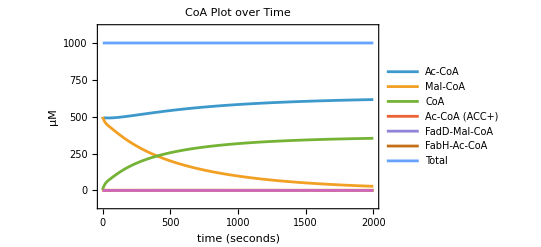

```mathematica
labelsCoA={"Ac-CoA","Mal-CoA","CoA","Ac-CoA (ACC+)","FadD-Mal-CoA","FabH-Ac-CoA","Total"};
Plot[
Evaluate[
If[ModelYear=="2020",
{y3[t],y8[t],y9[t],y86[t],y87[t],y90[t],y3[t]+y8[t]+y9[t]+y86[t]+y87[t]+y90[t]},
{y3[t],y8[t],y9[t],y86[t],y87[t],y90[t],y3[t]+y8[t]+y9[t]+y86[t]+y87[t]+y90[t]+y305[t]+y308[t],y305[t],y308[t]}]/.tsol],{t,0,2000},
Frame->True,FrameLabel->{"time (seconds)","μM"},PlotLabel->"CoA Plot over Time",PlotRange->{{0,2000},{-100,1100}},PlotLegends->labelsCoA]
```

Plot the number of C-atoms in substrate and product.

{C-atoms in Substrates,C-atoms in Products,C-atoms Total}

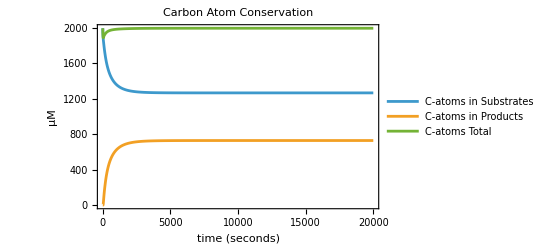

```mathematica
labelsC = {"C-atoms in Substrates","C-atoms in Products","C-atoms Total"}
Plot[Evaluate[{
y8[t]2+y3[t]2,
y16[t]4+y21[t]6+y26[t]8+y31[t]10+y37[t]12+y42[t]12+y47[t]14+y52[t]14+y57[t]16+y62[t]16+y67[t]18+y72[t]18+y77[t]20+y82[t]20,
y8[t]2+y3[t]2+y16[t]4+y21[t]6+y26[t]8+y31[t]10+y37[t]12+y42[t]12+y47[t]14+y52[t]14+y57[t]16+y62[t]16+y67[t]18+y72[t]18+y77[t]20+y82[t]20}/.tsol],{t,0,20000},
Frame->True,FrameLabel->{"time (seconds)", "μM"}, PlotLabel->"Carbon Atom Conservation",PlotLegends->labelsC]
```

```mathematica
If[DoZeroConcentrationsTest==True,
yvars=Table[Symbol["y"<>ToString[i]],{i,1,Length[importedODEs]}];
Assert[10^-10>=
Min[
Table[
Evaluate[Through[yvars[t]]/.tsol],{t,0,20000}] (* Through[] turns {y1, y2, ...} [t] into {y1[t], y2[t], ...} *)
]>=-10^-10];,
Print["Skipping zero check..."]
];
```

Plot fraction of saturated or unsaturated in total.

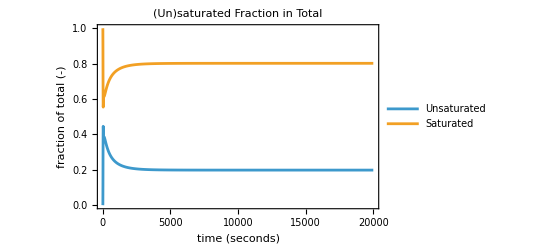

```mathematica
unsatFA={y32[t],(*C10ucisACP*)
y38[t],y39[t],y40[t],y41[t],y42[t],(*C12u*)
y48[t],y49[t],y50[t],y51[t],y52[t],(*C14u*)
y58[t],y59[t],y60[t],y61[t],y62[t],(*C16u*)
y68[t],y69[t],y70[t],y71[t],y72[t],(*C18u*)
y78[t],y79[t],y80[t],y81[t],y82[t]    (*C20u*)};
satFA={y12[t],y13[t],y14[t],y15[t],y16[t],(*C4*)
y17[t],y18[t],y19[t],y20[t],y21[t],(*C6*)
y22[t],y23[t],y24[t],y25[t],y26[t],(*C8*)
y27[t],y28[t],y29[t],y30[t],y31[t],(*C10*)
y33[t],y34[t],y35[t],y36[t],y37[t],(*C12*)
y43[t],y44[t],y45[t],y46[t],y47[t],(*C14*)
y53[t],y54[t],y55[t],y56[t],y57[t],(*C16*)
y63[t],y64[t],y65[t],y66[t],y67[t],(*C18*)
y73[t],y74[t],y75[t],y76[t],y77[t]    (*C20*)};
Plot[
Evaluate[
{Total[unsatFA]/(Total[unsatFA]+Total[satFA]),Total[satFA]/(Total[unsatFA]+Total[satFA])}/. tsol,
{t,0,20000}],
Frame->True,FrameLabel->{"time (seconds)","fraction of total (-)"},PlotLabel->"(Un)saturated Fraction in Total",PlotLegends->{"Unsaturated","Saturated"}]
```

## Flux Analysis

Step 1: Import the ODEs with the rates (generated by the ‘mass_action_in_rates.py’ script) and the mappings from the rate to expression.

```mathematica
ODEsPath=FileNameJoin[{NotebookDirectory[], "data/FAS/YEAR_fox_ODEs_in_rates.xlsx"}]//StringReplace["YEAR"->ModelYear];
importedODEsRates = Import[ODEsPath, "XLSX"][[1]][[2;;,3]];  (* Sheet, Row, Col *)
importedNetRatesToFBRates = Import[ODEsPath, "XLSX"][[3]][[2;;,{1,2}]];
importedFBRatesToExpr=Import[ODEsPath, "XLSX"][[2]][[2;;,{1,2}]];
ODEsRates = ToExpression[StringReplace[#,{"[t] ="->"'[t] ==", "_"->"","("->"",")"->""}]]&/@importedODEsRates;
rateNetToRateFBMap=Rule[
ToExpression[StringReplace[#[[1]],{"_"->"","("->"",")"->""}]],
ToExpression[StringReplace[#[[2]],{"_"->"","("->"",")"->""}]]]&/@importedNetRatesToFBRates;
rateFBToExprMap=Rule[
ToExpression[StringReplace[#[[1]],{"_"->"","("->"",")"->""}]],
ToExpression[StringReplace[#[[2]],{"_"->"","("->"",")"->""}]]]&/@importedFBRatesToExpr;
ODEsRates[[1;;5]] /.rateNetToRateFBMap /.rateFBToExprMap //TableForm
ODEs[[1;;5]]//TableForm (* A quick comparison to see if the equations are correct *)
Assert[ToString[ODEsRates /.rateNetToRateFBMap /.rateFBToExprMap]== ToString[ODEs]]
```

y1'[t]==-k11f e1[t] y1[t]+k11r y83[t]
y2'[t]==-k12f y2[t] y83[t]+k12r y84[t]
y3'[t]==-k104f e10[t] y3[t]-k31f e3[t] y3[t]-k84f e8[t] y3[t]+k104r y305[t]+k84r y308[t]-k13f y3[t] y85[t]+k13r y86[t]+k31r y90[t]
y4'[t]==kcat71 y101[t]+k82f1 y102[t]+k102f1 y107[t]+kcat72 y116[t]+k82f2 y117[t]+k102f2 y122[t]+kcat73 y131[t]+k82f3 y132[t]+k102f3 y137[t]+kcat74 y146[t]+k82f4 y147[t]+k102f4 y152[t]+kcat75 y161[t]+k82f5 y162[t]+k102f5 y167[t]+kcat76 y176[t]+k82f6 y177[t]+k102f6 y182[t]+kcat77 y191[t]+k82f7 y192[t]+k102f7 y197[t]+kcat78 y206[t]+k82f8 y207[t]+k102f8 y212[t]+kcat79 y221[t]+kcat75 y230[t]+k82f5 y231[t]+k102f5 y236[t]+kcat76 y245[t]+k82f6 y246[t]+k102f6 y251[t]+kcat77 y260[t]+k82f7 y261[t]+k102f7 y266[t]+kcat78 y275[t]+k82f8 y276[t]+k102f8 y281[t]+kcat79 y290[t]+k3inhr y293[t]+k4inhr y294[t]+k5inhr y295[t]+k6inhr y296[t]+k7inhr y297[t]+k8inhr y298[t]+k9inhr y299[t]+k10inhr y300[t]+k102f4 y302[t]+k109f y313[t]+k89f y315[t]-k10inhf e10[t] y4[t]-k3inhf e3[t] y4[t]-k4inhf e4[t] y4[t]-k5inhf e5[t] y4[t]-k6inhf e6[t] y4[t]-k7inhf e7[t] y4[t]-k8inhf e8[t] y4[t]-k9inhf e9[t] y4[t]-k82r1 y103[t] y4[t]-k102r1 y108[t] y4[t]-k82r2 y118[t] y4[t]-k102r2 y123[t] y4[t]-k82r3 y133[t] y4[t]-k102r3 y138[t] y4[t]-k82r4 y148[t] y4[t]-k102r4 y153[t] y4[t]-k82r5 y163[t] y4[t]-k102r5 y168[t] y4[t]-k82r6 y178[t] y4[t]-k102r6 y183[t] y4[t]-k82r7 y193[t] y4[t]-k102r7 y198[t] y4[t]-k82r8 y208[t] y4[t]-k102r8 y213[t] y4[t]-k82r5 y232[t] y4[t]-k102r5 y237[t] y4[t]-k82r6 y247[t] y4[t]-k102r6 y252[t] y4[t]-k82r7 y262[t] y4[t]-k102r7 y267[t] y4[t]-k82r8 y277[t] y4[t]-k102r8 y282[t] y4[t]-k102r4 y303[t] y4[t]-k109r y306[t] y4[t]-k89r y309[t] y4[t]-k23f y4[t] y88[t]+k23r y89[t]
y5'[t]==-k41f1 e4[t] y5[t]+k41r1 y93[t]

y1'[t]==-k11f e1[t] y1[t]+k11r y83[t]
y2'[t]==-k12f y2[t] y83[t]+k12r y84[t]
y3'[t]==-k104f e10[t] y3[t]-k31f e3[t] y3[t]-k84f e8[t] y3[t]+k104r y305[t]+k84r y308[t]-k13f y3[t] y85[t]+k13r y86[t]+k31r y90[t]
y4'[t]==kcat71 y101[t]+k82f1 y102[t]+k102f1 y107[t]+kcat72 y116[t]+k82f2 y117[t]+k102f2 y122[t]+kcat73 y131[t]+k82f3 y132[t]+k102f3 y137[t]+kcat74 y146[t]+k82f4 y147[t]+k102f4 y152[t]+kcat75 y161[t]+k82f5 y162[t]+k102f5 y167[t]+kcat76 y176[t]+k82f6 y177[t]+k102f6 y182[t]+kcat77 y191[t]+k82f7 y192[t]+k102f7 y197[t]+kcat78 y206[t]+k82f8 y207[t]+k102f8 y212[t]+kcat79 y221[t]+kcat75 y230[t]+k82f5 y231[t]+k102f5 y236[t]+kcat76 y245[t]+k82f6 y246[t]+k102f6 y251[t]+kcat77 y260[t]+k82f7 y261[t]+k102f7 y266[t]+kcat78 y275[t]+k82f8 y276[t]+k102f8 y281[t]+kcat79 y290[t]+k3inhr y293[t]+k4inhr y294[t]+k5inhr y295[t]+k6inhr y296[t]+k7inhr y297[t]+k8inhr y298[t]+k9inhr y299[t]+k10inhr y300[t]+k102f4 y302[t]+k109f y313[t]+k89f y315[t]-k10inhf e10[t] y4[t]-k3inhf e3[t] y4[t]-k4inhf e4[t] y4[t]-k5inhf e5[t] y4[t]-k6inhf e6[t] y4[t]-k7inhf e7[t] y4[t]-k8inhf e8[t] y4[t]-k9inhf e9[t] y4[t]-k82r1 y103[t] y4[t]-k102r1 y108[t] y4[t]-k82r2 y118[t] y4[t]-k102r2 y123[t] y4[t]-k82r3 y133[t] y4[t]-k102r3 y138[t] y4[t]-k82r4 y148[t] y4[t]-k102r4 y153[t] y4[t]-k82r5 y163[t] y4[t]-k102r5 y168[t] y4[t]-k82r6 y178[t] y4[t]-k102r6 y183[t] y4[t]-k82r7 y193[t] y4[t]-k102r7 y198[t] y4[t]-k82r8 y208[t] y4[t]-k102r8 y213[t] y4[t]-k82r5 y232[t] y4[t]-k102r5 y237[t] y4[t]-k82r6 y247[t] y4[t]-k102r6 y252[t] y4[t]-k82r7 y262[t] y4[t]-k102r7 y267[t] y4[t]-k82r8 y277[t] y4[t]-k102r8 y282[t] y4[t]-k102r4 y303[t] y4[t]-k109r y306[t] y4[t]-k89r y309[t] y4[t]-k23f y4[t] y88[t]+k23r y89[t]
y5'[t]==-k41f1 e4[t] y5[t]+k41r1 y93[t]

Step 2: Formulate the v and the r to calculate  r = S^T * v = 0  later.

```mathematica
vectorMetabs=Symbol[StringReplace[ToString[#],{"'[t]"->""}]]&/@ODEsRates[[All,1]]; (* The y's of the metabolites *)
vectorR=ODEsRates[[All,2]]; (* The right-hand side of the ODEs *)
vectorV=DeleteDuplicates[Cases[vectorR,_Symbol,All]]; (* The number of unique v's *)
(* Cases searches through and returns all patterns that match a pattern *)
(* The pattern at hand is any symbol (_Symbol), because we know there are only v's in the equations *)
vectorMetabs[[1;;5]]//TableForm
vectorR[[1;;5]]//TableForm
vectorV[[1;;5]]//TableForm
```

y1
y2
y3
y4
y5

-v11
-v12
-v104-v13-v31-v84
v1021+v1022+v1023+v1024+v1024d+v1025+v1025d+v1026+v1026d+v1027+v1027d+v1028+v1028d+v109-v10inh-v23-v3inh-v4inh-v5inh-v6inh-v7inh+v821+v822+v823+v824+v825+v825d+v826+v826d+v827+v827d+v828+v828d+v89-v8inh-v9inh+vcat71+vcat72+vcat73+vcat74+vcat75+vcat75d+vcat76+vcat76d+vcat77+vcat77d+vcat78+vcat78d+vcat79+vcat79d
-v411

v11
v12
v104
v13
v31

Step 3: Calculate the stoichiometric matrix (S), the NullSpace of S (K) and the NullSpace of S.T (L0).

```mathematica
augmentMatrixS[S_,metabs_]:=Module[{importExportEqs,externalIndices,exchangeCols},
importExportEqs=Import[FileNameJoin[{NotebookDirectory[], "data/FAS/fox_import_export_equations.csv"}]];
vectorMetabsExt=Symbol/@importExportEqs[[All,2]];
externalIndices=Flatten[Position[metabs,#]&/@vectorMetabsExt];
exchangeCols=Table[
Module[{col=ConstantArray[0,Length[metabs]],dir},
dir=importExportEqs[[k,3]]; (* "in" or "out" *)
col[[externalIndices[[k]]]]=If[dir=="in",1,-1];
col],
{k,Length[externalIndices]}];
matrixSaug=Join[S,Transpose[exchangeCols],2];
vectorVaug=Join[vectorV,Symbol[StringReplace[#,{"_"->""}]]&/@importExportEqs[[All,1]]];
Print["External metabolites: ",vectorMetabsExt, "(" <> ToString[Length[vectorMetabsExt]] <>")"];
Print["Augmented S-matrix: " <> ToString[Dimensions[matrixSaug]]]
]
matrixS=Normal[CoefficientArrays[vectorR, vectorV][[2]]];
Assert[MatrixQ[matrixS]==True];
matrixKint=NullSpace[matrixS];
matrixL0int=NullSpace[matrixS//Transpose];
augmentMatrixS[matrixS,vectorMetabs];
matrixK=NullSpace[matrixSaug];
matrixL0=NullSpace[matrixSaug//Transpose];
Print["Dimensions S: " <> ToString[Dimensions[matrixS]] <> 
", Rank: " <> ToString[MatrixRank[matrixS]] <> 
", Dimensions Null(S): " <> ToString[Dimensions[matrixKint]] <> 
", Dimensions Null(S.T): " <> ToString[Dimensions[matrixL0int]]<>
", Dimensions Null(Saug): " <> ToString[Dimensions[matrixK]] <>
", Dimensions Null(Saug.T): " <> ToString[Dimensions[matrixL0]]];
If[DoExports[[1]]==True,(* TODO: Accomodate S-augmented change! *)
vectorMetabsStr=ToString/@vectorMetabs;
vectorMetabsIntStr=ToString/@vectorMetabsInt;
vectorVaugStr=ToString/@vectorVaug;
vectorVStr=ToString/@vectorV;
Export["./scripts/efm_script/input/YEAR_S_matrix.mat"//StringReplace["YEAR"->ModelYear],{"S"->matrixS,"metabs"->vectorMetabsStr,"v"->vectorVStr}];
Export["./scripts/efm_script/input/YEAR_Saug_matrix.mat"//StringReplace["YEAR"->ModelYear],{"S"->matrixSaug,"metabs"->vectorMetabsStr,"v"->vectorVaugStr}];
Print["Exporting S.mat and Saug.mat to './scripts/efm_script/input/'..."],
Print["Skipping Export[]..."]]
```

External metabolites: {y1,y2,y3,y5,y6,y7,y9,y11,y16,y21,y26,y31,y37,y42,y47,y52,y57,y62,y67,y72,y77,y82}(22)

Augmented S-matrix: {315, 359}

Dimensions S: {315, 337}, Rank: 307, Dimensions Null(S): {30, 337}, Dimensions Null(S.T): {8, 315}, Dimensions Null(Saug): {45, 359}, Dimensions Null(Saug.T): {1, 315}

Skipping Export[]...

Step 4: Get model in “reactions” form: v1 == y1 - y2. Can maybe be checked using Frank’s package (in “FoxModelStoichioCheck.nb”)

```mathematica
reactions=#[[1]]==Total[#[[2]]]&/@
Table[
Module[{flux=vectorVaug[[j]],extQ},
extQ=StringMatchQ[SymbolName[flux],"vin*"|"vout*"];
{flux,
DeleteCases[
Table[
If[matrixSaug[[i,j]]!=0,
matrixSaug[[i,j]]*
If[extQ,
vectorMetabs[[i]]-ToExpression["$"<>SymbolName[vectorMetabs[[i]]]],
vectorMetabs[[i]]],
Nothing
],
{i,Length[vectorMetabs]}
],
Nothing
]
}
],
{j,Length[vectorVaug]}];
reactions[[{1,2,3,Length[vectorVaug],Length[vectorVaug]-1,Length[vectorV]+1}]]//TableForm
If[DoExports[[3]]==True,
reactionsStr=ToString[#,InputForm]&/@reactions;
Export[FileNameJoin[{"./raw_output/YEAR_fox_reactions.csv"}]//StringReplace["YEAR"->ModelYear],reactionsStr,"CSV"],
Print["Skipping reactions Export[]..."]]
```

v11==-y1+y83
v12==-y2-y83+y84
v104==-y3+y305
vout82==-y82+$y82
vout77==-y77+$y77
vin1==y1-$y1

Skipping reactions Export[]...

Step 4.2: Get the conserved moieties by augmenting the S-matrix with the identity matrix and performing Gaussian elimination. This is the same as the L0 matrix!

```mathematica
(* Analysis according to: doi:10.1006/jtbi.2002.2547 *)
GetMoietiesMatrix[matrix_]:=Module[{n,m, augMatrix,rr,rrAug,rrMat},
{n,m} =Dimensions[matrix];
augMatrix=Join[matrix, IdentityMatrix[n], 2]; (* Create an [n x (m + n)] augmented matrix by joining S and I along the columns "2" *)
rr=Normal[RowReduce[augMatrix]]; (* Row reduce the matrix *)
rrAug=Normal[rr[[All,m+1;;m+n]]];
rrMat=Normal[rr[[All,1;;m]]];
Return[{rrMat,rrAug}]
]
```

Step 5: To label the matrix rows and columns correctly the independent and dependent variables have to be found.

```mathematica
metabConservations=matrixL0 . vectorMetabs;
metabConservations=#==Constant&/@metabConservations;
metabConservations//TableForm
fluxConservations=matrixK . vectorVaug;
fluxConservations = # == Constant & /@ fluxConservations;
(* Export the conservations to an Excel *)
If[DoExports[[2]]==True,
metabConservationsStr=ToString[#,InputForm]&/@metabConservations;
Export[FileNameJoin[{"./raw_output/YEAR_fox_metabolite_conservations.xlsx"}]//StringReplace["YEAR"->ModelYear],metabConservationsStr,"XLSX"];
fluxConservationsStr=ToString[#, InputForm] &/@fluxConservations;
Export[FileNameJoin[{"./raw_output/YEAR_fox_metabolite_conservations.xlsx"}]//StringReplace["YEAR"->ModelYear],fluxConservationsStr,"XLSX"];
Print["Exported metabolite and flux conservations..."],
Print["Skipping Export[]..."]
];
```

y10+y100+y101+y102+y104+y105+y106+y107+y109+y110+y111+y112+y113+y114+y115+y116+y117+y119+y12+y120+y121+y122+y124+y125+y126+y127+y128+y129+y13+y130+y131+y132+y134+y135+y136+y137+y139+y14+y140+y141+y142+y143+y144+y145+y146+y147+y149+y15+y150+y151+y152+y154+y155+y156+y157+y158+y159+y160+y161+y162+y164+y165+y166+y167+y169+y17+y170+y171+y172+y173+y174+y175+y176+y177+y179+y18+y180+y181+y182+y184+y185+y186+y187+y188+y189+y19+y190+y191+y192+y194+y195+y196+y197+y199+y20+y200+y201+y202+y203+y204+y205+y206+y207+y209+y210+y211+y212+y214+y215+y216+y217+y218+y219+y22+y220+y221+y222+y223+y224+y225+y226+y227+y228+y229+y23+y230+y231+y233+y234+y235+y236+y238+y239+y24+y240+y241+y242+y243+y244+y245+y246+y248+y249+y25+y250+y251+y253+y254+y255+y256+y257+y258+y259+y260+y261+y263+y264+y265+y266+y268+y269+y27+y270+y271+y272+y273+y274+y275+y276+y278+y279+y28+y280+y281+y283+y284+y285+y286+y287+y288+y289+y29+y290+y291+y292+y293+y294+y295+y296+y297+y298+y299+y30+y300+y301+y302+y304+y307+y310+y311+y312+y313+y314+y315+y32+y33+y34+y35+y36+y38+y39+y4+y40+y41+y43+y44+y45+y46+y48+y49+y50+y51+y53+y54+y55+y56+y58+y59+y60+y61+y63+y64+y65+y66+y68+y69+y70+y71+y73+y74+y75+y76+y78+y79+y80+y81+y89+y92+y95+y96+y97+y98+y99==Constant

Skipping Export[]...

Step 6: Overall reaction

```mathematica
reactionRules=reactions/.Equal->Rule;
overalls=Simplify[matrixK . vectorVaug]/.reactionRules;
formatReaction[expr_]:=Module[{rules,substrates,products,formatSide},
(* If the entry is 0, skip it *)
If[expr===0,Return["0"]];
(* Extract coefficients and variable names *)
rules=CoefficientRules[expr,Variables[expr]];
vars=Variables[expr];
(* Separate into Left and Right based on the sign of the coefficient *)
substrates=Select[rules,Last[#]<0&];
products=Select[rules,Last[#]>0&];
(* Helper to turn lists into "2 y1 + y2" strings *)
formatSide[list_]:=StringRiffle[
Map[
Function[rule,
With[{coeff=Abs[Last[rule]],
name=vars[[Position[First[rule],1][[1,1]]]]},
If[coeff==1,ToString[name],ToString[coeff]<>" "<>ToString[name]]]],
list]," + "];
(* Join sides with the arrow *)
formatSide[substrates]<>" => "<>formatSide[products]];

(* Apply to your vector *)
formattedReactions=Select[formatReaction/@overalls,#!="0"&];

(* Display as column *)
Column[formattedReactions]
If[DoExports[[4]]==True,
Export[FileNameJoin["./raw_output/YEAR_fox_overall_reactions.xlsx"]//StringReplace["YEAR"->ModelYear],formattedReactions,"XLSX"];
Print["Exported Overall Reactions"],
Print["Skipping Overall Reactions Export[]..."]]
```

10 $y3 + 9 $y5 + 8 $y6 => $y82 + 10 $y9
10 $y3 + 9 $y5 + 9 $y6 => $y77 + 10 $y9
9 $y3 + 8 $y5 + 7 $y6 => $y72 + 9 $y9
9 $y3 + 8 $y5 + 8 $y6 => $y67 + 9 $y9
8 $y3 + 7 $y5 + 6 $y6 => $y62 + 8 $y9
8 $y3 + 7 $y5 + 7 $y6 => $y57 + 8 $y9
7 $y3 + 6 $y5 + 5 $y6 => $y52 + 7 $y9
7 $y3 + 6 $y5 + 6 $y6 => $y47 + 7 $y9
6 $y3 + 5 $y5 + 4 $y6 => $y42 + 6 $y9
6 $y3 + 5 $y5 + 5 $y6 => $y37 + 6 $y9
5 $y3 + 4 $y5 + 4 $y6 => $y31 + 5 $y9
4 $y3 + 3 $y5 + 3 $y6 => $y26 + 4 $y9
3 $y3 + 2 $y5 + 2 $y6 => $y21 + 3 $y9
2 $y3 + $y5 + $y6 => $y16 + 2 $y9
$y1 + $y2 => $y11 + $y7

Skipping Overall Reactions Export[]...